```mathematica
Quit[];
```

total number of errors and warnings
===================================
fferr: 14650 times ffxc0: lambda(p1,p2,p3) < 0, unphysical configuration

```mathematica
(*$LoadAddOns={"FeynArts"};
Get["FeynCalc`"]*)
(*<<X`*)
(*Needs["CollierLink`"]*)
(*<<CollierLink`*)
Needs["CollierLink`"]
Install["LoopTools"]
Needs["LoopTools`"]
(*Needs["CollierLink`"]*)
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

CollierLink v1.0.1, by Hiren H. Patel
For more information, see the

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

LinkObject[…]

```mathematica
GV[ga_,Q_]:=ga*(1-4*Abs[Q]*sw^2);


Particles=Association[];
AppendTo[Particles,e->{0.511*10^(-6),-1,-1/2,GV[-1/2,-1],1}];
AppendTo[Particles,mu->{105.66*10^(-6),-1,-1/2,GV[-1/2,-1],1}];
AppendTo[Particles,tau->{1.78*10^(-3),-1,-1/2,GV[-1/2,-1],1}];
AppendTo[Particles,n->{0,0,1/2,GV[1/2,0],1}];
AppendTo[Particles,u->{2.01*10^(-6),2/3,1/2,GV[1/2,2/3],3}];
AppendTo[Particles,d->{4.79*10^(-6),-1/3,-1/2,GV[-1/2,-1/3],3}];
AppendTo[Particles,c->{1.25*10^(-3),2/3,1/2,GV[1/2,2/3],3}];
AppendTo[Particles,sq->{95*10^(-6),-1/3,-1/2,GV[-1/2,-1/3],3}];
AppendTo[Particles,t->{173.1*10^(-3),2/3,1/2,GV[1/2,2/3],3}];
AppendTo[Particles,b->{4.67*10^(-3),-1/3,-1/2,GV[-1/2,-1/3],3}];

mz=91.187*10^(-3);
mw=80.385*10^(-3);
v=246.22*10^(-3);

cw=mw/mz;
sw=Sqrt[1-cw^2];
g=2*mw/v;
q=g*sw;
(*
B0[s_,mi_,mj_]:=PVB[0,0,s,mi,mj];
BZ[s_,mi_,mj_]:=PVB[0,0,s,mi,mj] - PVB[0,0,mz^2 ,mi,mj];
CZZ[s_,mi_,mj_,mk_]:=PVC[0,0,0,mz^2,mz^2,s,mi,mj,mk];
CZg[s_,mi_,mj_,mk_]:=PVC[0,0,0,mz^2,0,s,mi,mj,mk];
*)
(*B0 определен так же*)
BZ[s_,mi_,mj_]:=B0[s,mi^2,mj^2] - B0[mz^2 ,mi^2,mj^2];
CZZ[s_,mi_,mj_,mk_]:=C0[mz^2,mz^2,s,mi^2,mj^2,mk^2];
CZg[s_,mi_,mj_,mk_]:=C0[mz^2,0,s,mi^2,mj^2,mk^2];

H3g[s_,M_,Q_,ga_,gv_,Nf_]:=(Nf*q^2*Q^2 * ga/(4*Pi^2 *cw*sw))(mz^2/(s-mz^2))(1+2M^2CZg[s,M,M,M] + (mz^2/(s-mz^2))BZ[s,M,M]);
H3Z[s_,M_,Q_,ga_,gv_,Nf_]:=(Nf*q^2*Q*gv*ga/(4Pi^2 sw^2 cw^2))(mz^2/(s-mz^2)^2)((s*mz^2)/(s-mz^2)BZ[s,M,M] + ((s+mz^2)/2) (2CZg[s,M,M,M]M^2+1))
F5g[s_,M_,Q_,ga_,gv_,Nf_]:=-(Nf*q^2*Q*ga*gv/(8Pi^2sw^2cw^2s))(mz^2/(s-4mz^2)^2)(2BZ[s,M,M]mz^2(s+2mz^2)+(s-2mz^2)(s-4mz^2)+2CZZ[s,M,M,M](M^2(s-4mz^2)(s-2mz^2)+2mz^4(s-mz^2)));
F5Z[s_,M_,Q_,ga_,gv_,Nf_]:=-(Nf*q^2ga/(16Pi^2sw^3cw^3))(mz^2/(s-4mz^2)^2)((3gv^2+ga^2)(s-4mz^2)/3+(BZ[s,M,M]/(s-mz^2))(4ga^2M^2(s-4mz^2)+(3gv^2+ga^2)mz^2(s+2mz^2))+2CZZ[s,M,M,M](gv^2+ga^2)M^2(s-4mz^2)+mz^4(3gv^2+ga^2))


CDist[s_,M_,Q_,ga_,gv_,Nf_]:=F5g[s,M,Q,ga,gv,Nf]

Quarks[s_]:=CDist[s,2.01*10^(-6),2/3,1/2,GV[1/2,2/3],3]+CDist[s,4.79*10^(-6),-1/3,-1/2,GV[-1/2,-1/3],3]+CDist[s,95*10^(-6),-1/3,-1/2,GV[-1/2,-1/3],3]+CDist[s,1.25*10^(-3),2/3,1/2,GV[1/2,2/3],3]+CDist[s,4.67*10^(-3),-1/3,-1/2,GV[-1/2,-1/3],3];
Leptons[s_]:=CDist[s,0.511*10^(-6),-1,-1/2,GV[-1/2,-1],1]+CDist[s,105.66*10^(-6),-1,-1/2,GV[-1/2,-1],1]+CDist[s,1.78*10^(-3),-1,-1/2,GV[-1/2,-1],1]+3CDist[s,0,0,1/2,GV[1/2,0],1];
TQuark[s_]:=CDist[s,173.1*10^(-3),2/3,1/2,GV[1/2,2/3],3];

Tot [s_]:=Quarks[s]+Leptons[s]+TQuark[s];
(*Tot[0.2^2]*)
(*Tot[0.5^2]*)
(*Tot[7^2]*)
(*Tot[8^2]*)
Sqrt[Re[Tot[13^2]]^2+Im[Tot[13]]^2]
(*Tot[14^2]*)


(*Plot[{Re[Quarks[s^2]],Re[Leptons[s^2]],Re[Tot[s^2]],Re[TQuark[s^2]],Im[TQuark[s^2]]},{s,0.1,1},PlotRange->{{0.1,1},{-0.0018,0.0005}}]*)
(*Plot[Re[H3g[8^2,m,2/3,1/2,GV[1/2,2/3],3]],{m,0,10^(1)}]
H3g[8^2,0.173*10^(-3),2/3,1/2,GV[1/2,2/3],3]*)
```

7.58148×10^-8

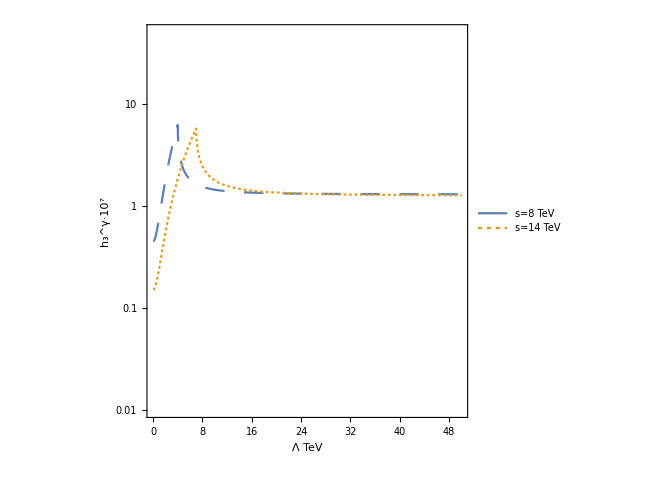

-4.08633×10^-6+0.0000275668 ⅈ

9.51216×10^-9

5.92584×10^-9

1.04677×10^-9

8.02071×10^-10

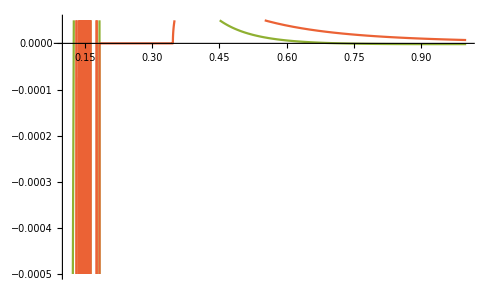

```mathematica
tgB=3;
mu=316*10^(-3);
(*M2=152*10^(-3);*)
(*M2=9*10^(2)*)

cosB=1/Sqrt[1+tgB^2];
sinB=tgB/Sqrt[1+tgB^2];
(*sinB = Sqrt[1-cosB^2];*)
sin2B=2*sinB*cosB;
cos2B=(cosB^2-sinB^2);
DD[M2_]:=Sqrt[(M2^2+mu^2+2*mw^2)^2-4*(M2*mu-mw^2*sin2B)^2];
sin2fR[M2_]:=(-2)*Sqrt[2]*mw*(mu*cosB+M2*sinB)/DD[M2];
sin2fL[M2_]:=(-2)*Sqrt[2]*mw*(mu*sinB+M2*cosB)/DD[M2];
cos2fR[M2_]:=(-1)*(M2^2-mu^2+2*cos2B*mw^2);
cos2fL[M2_]:=(-1)*(M2^2-mu^2-2*cos2B*mw^2);

gv1[M2_]:=3/2-2*sw^2+(1/4)*(cos2fL[M2]+cos2fR[M2]);
ga1[M2_]:=-(1/4)*(cos2fL[M2]-cos2fR[M2]);
gv2[M2_]:=3/2-2*sw^2-(1/4)*(cos2fL[M2]+cos2fR[M2]);
ga2[M2_]:=(1/4)*(cos2fL[M2]-cos2fR[M2]);
gv12[M2_]:=-Sign[M2]/4*(Sign[(M2*mu-sin2B*mw^2)]*sin2fR[M2]+sin2fL[M2]);
ga12[M2_]:=-Sign[M2]/4*(Sign[(M2*mu-sin2B*mw^2)]*sin2fR[M2]-sin2fL[M2]);

Mchi1[M2_]:=Sqrt[1/2*(M2^2+mu^2+2*mw^2-DD[M2])];
Mchi2[M2_]:=Sqrt[1/2*(M2^2+mu^2+2*mw^2+DD[M2])];

H3Z2[s_,M1_,M2_,Q_,ga_,gv_,Nf_]:=(Nf*q^2*Q*gv*ga/(4Pi^2 sw^2 cw^2))(mz^2/(s-mz^2)^2)((2s mz^2/(s-mz^2))BZ[s,M1,M2] +(s+mz^2)(M2^2 CZg[s,M1,M2,M2]+M1^2CZg[s,M2,M1,M1]+1))
F5g2[s_,M1_,M2_,Q_,ga_,gv_,Nf_]:=-(Nf*q^2*Q*ga*gv/(8Pi^2 sw^2 cw^2s))(mz^2/(s-4mz^2)^2)(4(s-mz^2)(M2^2-M1^2)(B0[s,M1^2,M1^2]-B0[s,M2^2,M2^2])+2(s-2mz^2)(s-4mz^2)+2mz^2(s+2mz^2)(B0[s,M1^2,M1^2]+B0[s,M2^2,M2^2]-2B0[mz^2,M1^2,M2^2])+4s(s-mz^2)(M1^4+M2^4+mz^4-2M1^2M2^2-2M1^2mz^2-2M2^2mz^2)(CZZ[s,M1,M2,M1]+CZZ[s,M2,M1,M2])+2s(s+2mz^2)(M2^2CZZ[s,M1,M2,M1]+M1^2CZZ[s,M2,M1,M2]))
CDist2[s_,M1_,M2_,Q_,ga_,gv_,Nf_]:=F5g2[s,M1,M2,Q,ga,gv,Nf]


MSSM1[s_,M22_]:=10CDist[s,Mchi1[M22],1,ga1[M22],gv1[M22],1]+10CDist[s,Mchi2[M22],-1,ga2[M22],gv2[M22],1];
MSSM2[s_,M2_]:=H3Z2[s,Mchi1[M2],Mchi2[M2],1,ga12[M2],gv12[M2],1]+10CDist[s,Mchi1[M2],1,ga1[M2],gv1[M2],1]+10CDist[s,Mchi2,-1,ga2[M2],gv2[M2],1];
(*MSSM3[s_,M2_]:=F5g2[s,Mchi1[M2],Mchi2[M2],1,ga12[M2],gv12[M2],1]+F5g2[s,Mchi2[M2],Mchi1[M2],-1,ga12[M2],gv12[M2],1]+10CDist[s,Mchi1[M2],1,ga1[M2],gv1[M2],1]+10CDist[s,Mchi2[M2],1,ga2[M2],gv2[M2],1];*)
(*MSSM1F[s_, M2_]:=H3Z2[s,Mchi1[M2],Mchi2[M2],1,ga12[M2],gv12[M2],1]+10CDist[s,Mchi1[M2],1,ga1[M2],gv1[M2],1]+10CDist[s,Mchi1[M2],-1,ga2[M2],gv2[M2],1] + Tot[s];*)
MSSM2F[s_, M2_]:=H3Z2[s,Mchi1[M2],Mchi2[M2],1,ga12[M2],gv12[M2],1]+10CDist[s,Mchi1[M2],1,ga1[M2],gv1[M2],1]+10CDist[s,Mchi1[M2],-1,ga2[M2],gv2[M2],1] + Tot[s];
MSSM3F[s_,M2_]:=F5g2[s,Mchi1[M2],Mchi2[M2],1,ga12[M2],gv12[M2],1]+F5g2[s,Mchi2[M2],Mchi1[M2],-1,ga12[M2],gv12[M2],1]+(*10CDist[s,Mchi1[M2],1,ga1[M2],gv1[M2],1]+*)10CDist[s,Mchi2[M2],1,ga2[M2],gv2[M2],1]+Tot[s];
MSSM3F2[s_,M2_]:=Sqrt[Re[MSSM3F[s,M2]]^2 +Im[MSSM3F[s,M2]]^2];
LogPlot[{MSSM3F2[8^2,M]10^(7),MSSM3F2[14^2,M]10^(7)},{M,0,50},AspectRatio->1,PlotRange-> {{0,50},{0.01,50}},(*GridLines->Automatic,*)PlotStyle->{Dashing[Large],Dashing[Tiny]},TicksStyle->Directive[Black,15],Frame->True,FrameLabel->{{Style[ToExpression["h_3^{\\gamma} \\cdot 10^7",TeXForm,HoldForm],22],None},{ToExpression["\\Lambda  \\rm{TeV}",TeXForm,HoldForm],None}},FrameStyle->Directive[Black,18],PlotLegends->Placed[{Style["s=8 TeV",18],Style["s=14 TeV",18]},{0.75,0.8}]]

(*Re[MSSM2F[1^2,20]]*)
MSSM3F[Sqrt[0.2],0.152]
Sqrt[Re[Tot[7^2]]^2+Im[Tot[7^2]]^2]
Sqrt[Re[Tot[8^2]]^2+Im[Tot[8^2]]^2]
Sqrt[Re[Tot[13^2]]^2+Im[Tot[13^2]]^2]
Sqrt[Re[Tot[14^2]]^2+Im[Tot[14^2]]^2]
Fulll7=MSSM3F[7^2,0.15]+Tot[7^2];
Fulll8=MSSM3F[8^2,0.15]+Tot[8^2];
Fulll13=MSSM3F[13^2,0.15]+Tot[13^2];
Fulll14=MSSM3F[14^2,0.15]+Tot[14^2];
Sqrt[Re[Fulll7]^2+Im[Fulll7]^2];
Sqrt[Re[Fulll8]^2+Im[Fulll8]^2];
Sqrt[Re[Fulll13]^2+Im[Fulll13]^2];
Sqrt[Re[Fulll14]^2+Im[Fulll14]^2];
MSSM1[7^2,0.15];
Tot[7^2];
(*a=-0.34+0.25I
b=0.25+0.62
Sqrt[Re[b^2]+Im[b^2]]
Sqrt[Re[a+b]^2+Im[a+b]^2]*)
(*MSSM2F[0.2^2,Mchi1,Mchi2]*)


Plot[{Re[MSSM2[s^2]],Im[MSSM2[s^2]],Re[Tot[s^2]],Im[Tot[s^2]]},{s,0.1,1},PlotRange->{{0.1,1},{-0.0005,0.00005}}]
```